```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

pt(W)>150 GeV no other cuts

```mathematica
(*namerun="Mnunu300"*)
namerun="ptW150"
```

ptW150

```mathematica
namefolder="mupem_to_nunuWpWm_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
ptnu=prova[4];
etanu=prova[5];
Mnunu=prova[15];
MWW =prova[14];
etaW=prova[13];
ptW=prova[11];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="WW_WpWm_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZ =prova[10];
etaWZZ=prova[6];
ptWZZ=prova[4];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalf =prova[10];
etaWZZmuhalf=prova[6];
ptWZZmuhalf=prova[4];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarter =prova[10];
etaWZZmuquarter=prova[6];
ptWZZmuquarter=prova[4];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuLePDF =prova[10];
etaWZZmuLePDF=prova[6];
ptWZZmuLePDF=prova[4];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalfLePDF =prova[10];
etaWZZmuhalfLePDF=prova[6];
ptWZZmuhalfLePDF=prova[4];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterLePDF =prova[10];
etaWZZmuquarterLePDF=prova[6];
ptWZZmuquarterLePDF=prova[4];



(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZptmu =prova[10];
etaWZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4","WW Eva mu=sqrtshat","WW Eva mu=sqrtshat/2","WW Eva mu=sqrtshat/4"};
plotstyle={Thick,Dashed,Dashed,Dashed}
```

{Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV";
```

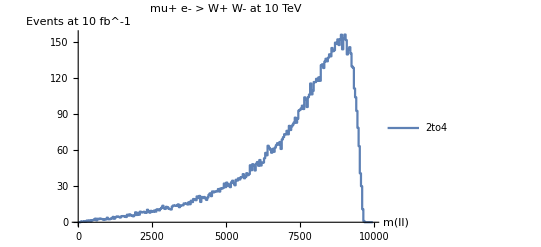

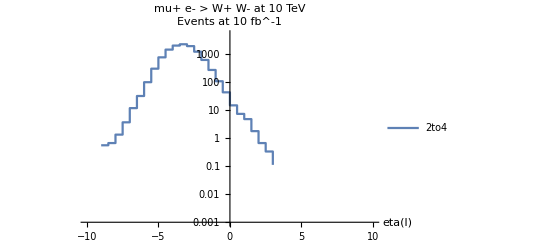

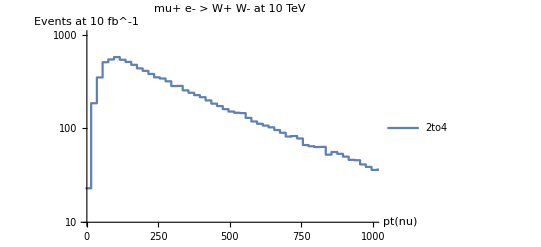

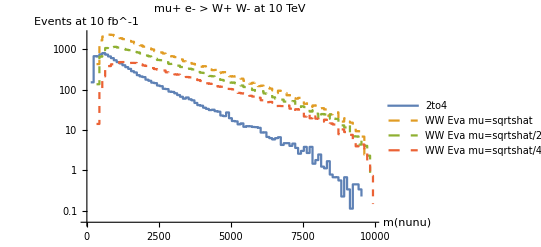

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

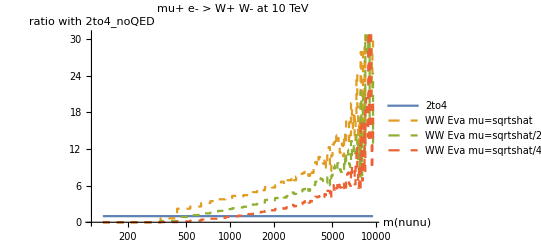

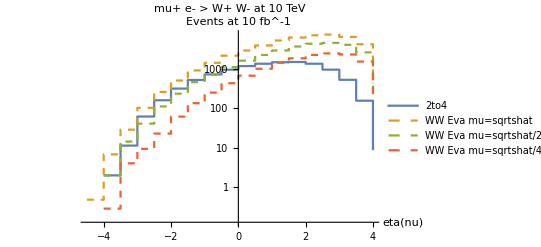

```mathematica
ListPlot[{joinbin[Mnunu,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etanu,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[ptnu,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] 


ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME","EVA mu=m(WW) with only Log[mu/MV]","EVA mu=m(WW)/2 with only Log[mu/MV]","EVA mu=m(WW)/4 with only Log[mu/MV]", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4"};
plotlegend2={"ME", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV, pt(W)>150 GeV";
```

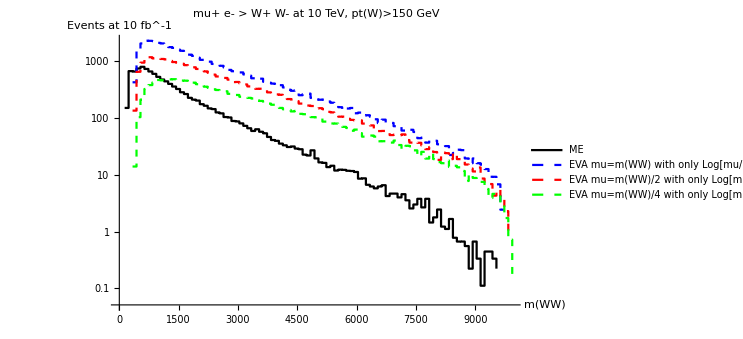

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

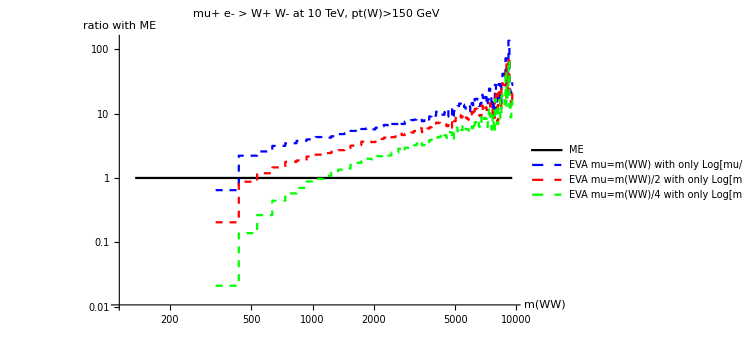

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

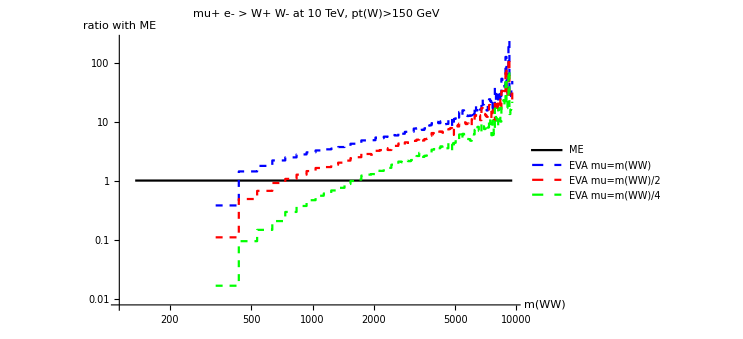

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

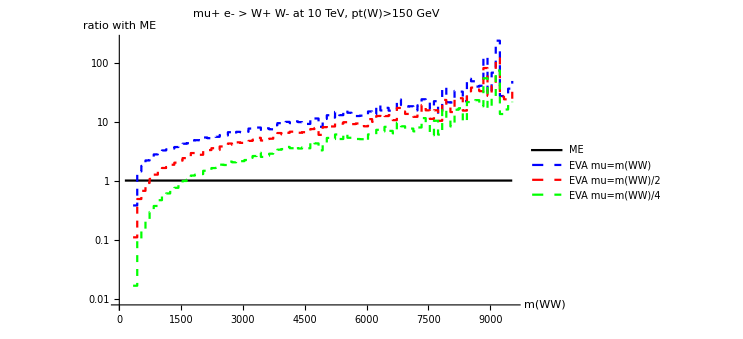

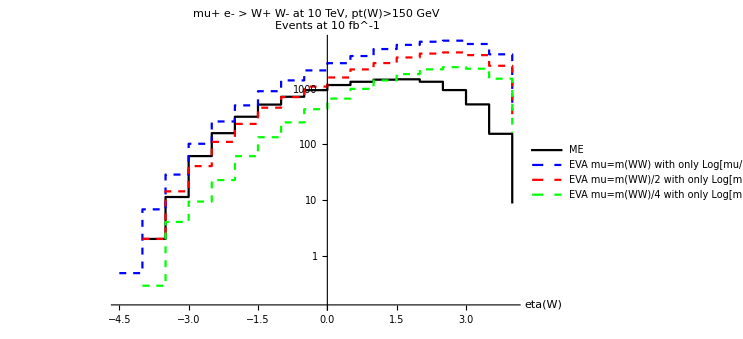

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

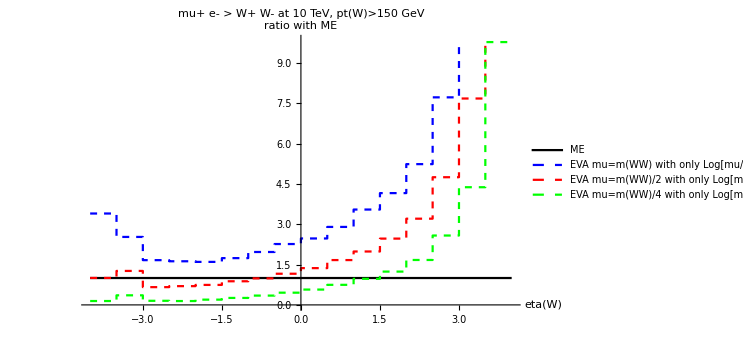

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

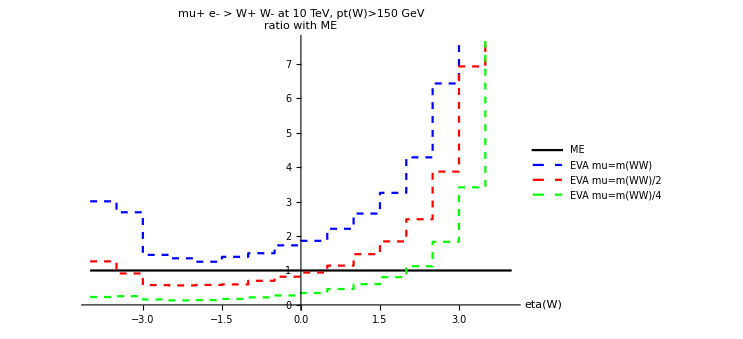

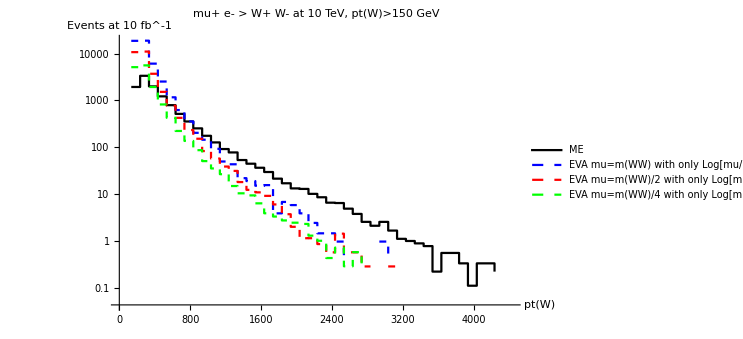

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

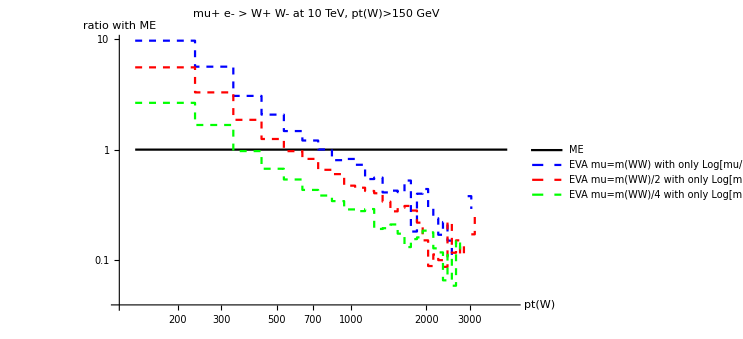

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

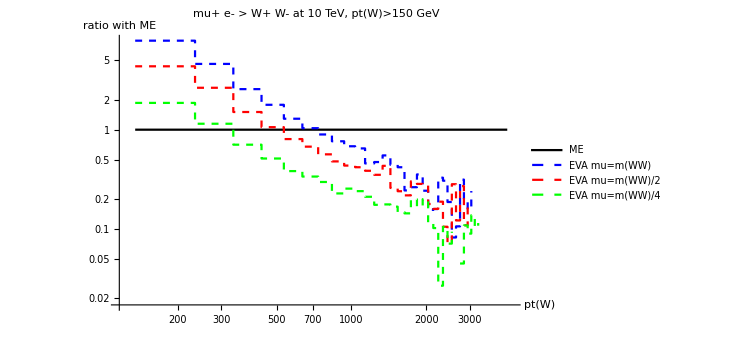

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

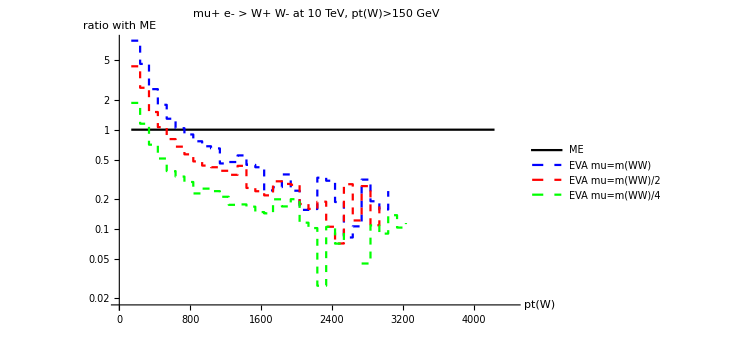

-Graphics-

```mathematica
plotmWW=ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio1=ListLogLogPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio2=ListLogLogPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalfLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterLePDF,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio2b=ListLogPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalfLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterLePDF,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 




plotetaW=ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio1=ListPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZ,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalf,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarter,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio2=ListPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalfLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarterLePDF,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 



plotptW=ListLogPlot[{joinbin[ptW,10],joinbin[ptWZZ,10],joinbin[ptWZZmuhalf,10],joinbin[ptWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"pt(W)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotptWratio1=ListLogLogPlot[{rapp[joinbin[ptW,10],joinbin[ptW,10]],rapp[joinbin[ptWZZ,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuhalf,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuquarter,10],joinbin[ptW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"pt(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotptWratio2=ListLogLogPlot[{rapp[joinbin[ptW,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuLePDF,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuhalfLePDF,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuquarterLePDF,10],joinbin[ptW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"pt(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550]

plotptWratio2b=ListLogPlot[{rapp[joinbin[ptW,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuLePDF,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuhalfLePDF,10],joinbin[ptW,10]],rapp[joinbin[ptWZZmuquarterLePDF,10],joinbin[ptW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"pt(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 


GraphicsColumn[{plotmWWratio2,plotptWratio2,plotetaWratio2}]

dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotDistr/WW_WW/";
run="10TeVolnlyptcut/";
Export[dir<>run<>"plotmWW.pdf",plotmWW];
Export[dir<>run<>"plotmWWratio1.pdf",plotmWWratio1];
Export[dir<>run<>"plotmWWratio2.pdf",plotmWWratio2];
Export[dir<>run<>"plotmWWratio2b.pdf",plotmWWratio2b];
Export[dir<>run<>"plotetaW.pdf",plotetaW];
Export[dir<>run<>"plotetaWratio1.pdf",plotetaWratio1];
Export[dir<>run<>"plotetaWratio2.pdf",plotetaWratio2];
Export[dir<>run<>"plotptW.pdf",plotptW];
Export[dir<>run<>"plotptWratio1.pdf",plotptWratio1];
Export[dir<>run<>"plotptWratio2.pdf",plotptWratio2];
Export[dir<>run<>"plotptWratio2b.pdf",plotptWratio2b];
```

```mathematica
Plus@@Map[#[[2]]&,etaW]
Plus@@Map[#[[2]]&,Mnunu]
Plus@@Map[#[[2]]&,MWW]
Plus@@Map[#[[2]]&,etaWZZ]
```

11168.2

11168.2

11168.2

48810.9

```mathematica
Plus@@Map[#[[2]]*#[[1]]&,ptnu]/Plus@@Map[#[[2]]&,ptnu]
Plus@@Map[#[[2]]&,ptnu]
```

402.625

11168.2

M(WW)>5000 GeV con anche Pt(W)> 1500 GeV e |eta(W)|<2.5. Collisioni a 100 TeV

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu5000_ptnu1500_eta2half"
suffix="_100TeV"
```

Mnunu5000_ptnu1500_eta2half

_100TeV

```mathematica
namefolder="mupem_to_nunuWpWm_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
ptnu=prova[4];
etanu=prova[5];
Mnunu=prova[15];
MWW =prova[14];
etaW=prova[13];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="WW_WpWm_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZ =prova[10];
etaWZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalf =prova[10];
etaWZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarter =prova[10];
etaWZZmuquarter=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuLePDF =prova[10];
etaWZZmuLePDF=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalfLePDF =prova[10];
etaWZZmuhalfLePDF=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterLePDF =prova[10];
etaWZZmuquarterLePDF=prova[6];



(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZptmu =prova[10];
etaWZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4","WW Eva mu=sqrtshat","WW Eva mu=sqrtshat/2","WW Eva mu=sqrtshat/4"};
plotstyle={Thick,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV";
```

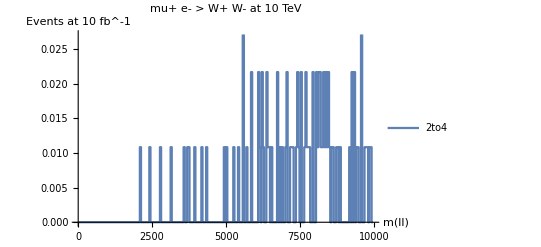

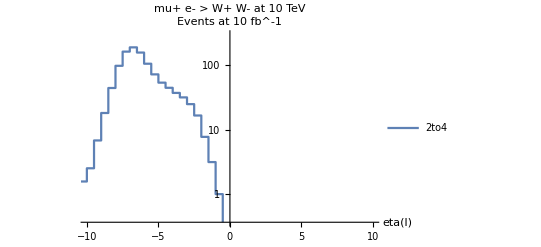

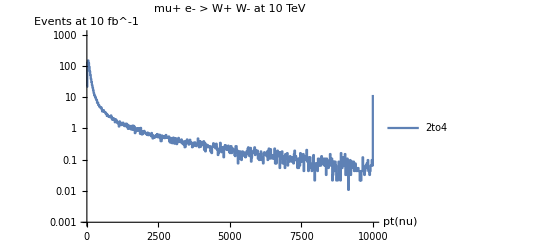

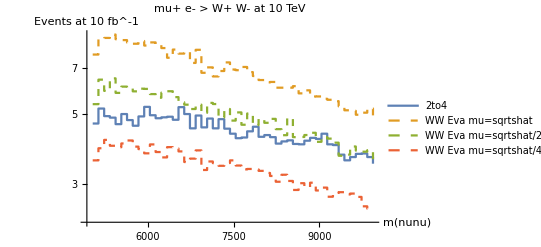

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

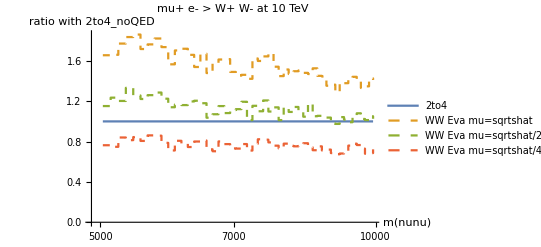

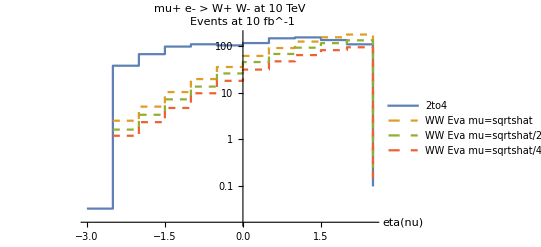

```mathematica
ListPlot[{joinbin[Mnunu,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etanu,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,300}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[ptnu,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,10000},{10^-3,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] 


ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME","EVA mu=m(WW) with only Log[mu/MV]","EVA mu=m(WW)/2 with only Log[mu/MV]","EVA mu=m(WW)/4 with only Log[mu/MV]", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4"};
plotlegend2={"ME", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > W+ W- at 100 TeV, M(WW)>5 TeV, Pt(W)> 1.5 TeV,|eta(W)|<2.5";
```

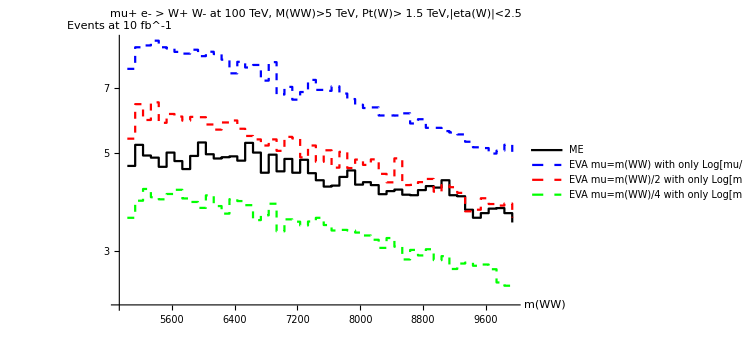

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

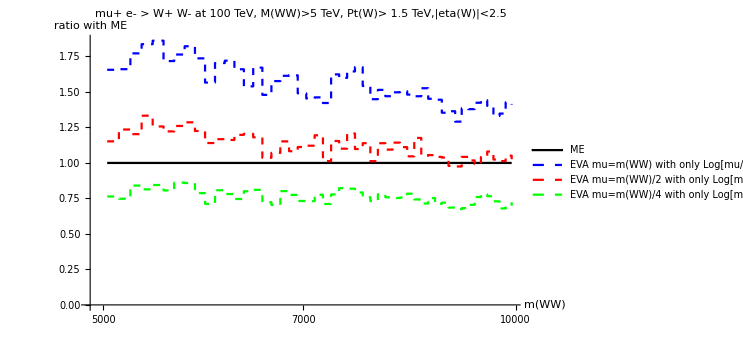

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

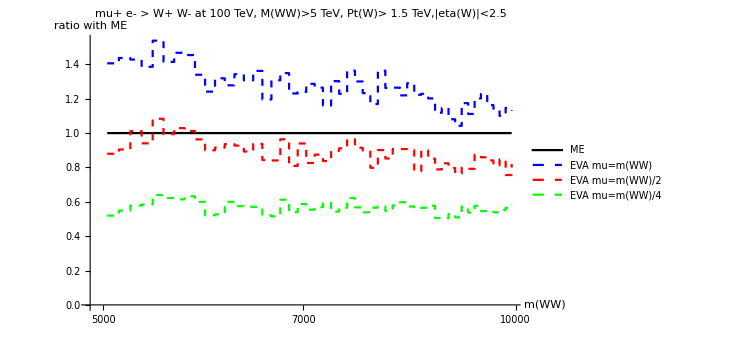

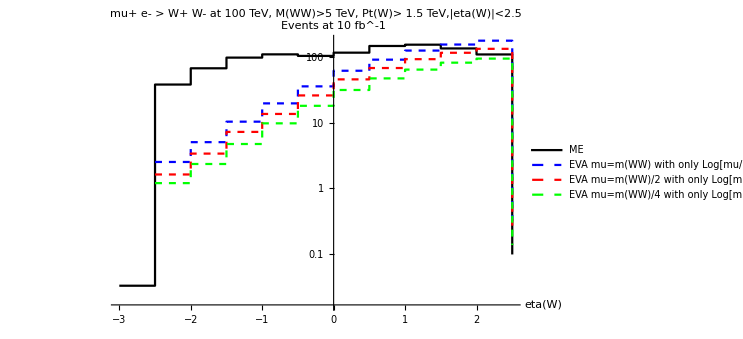

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

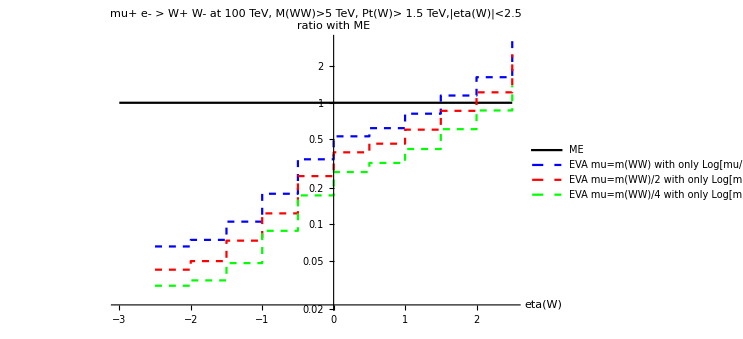

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

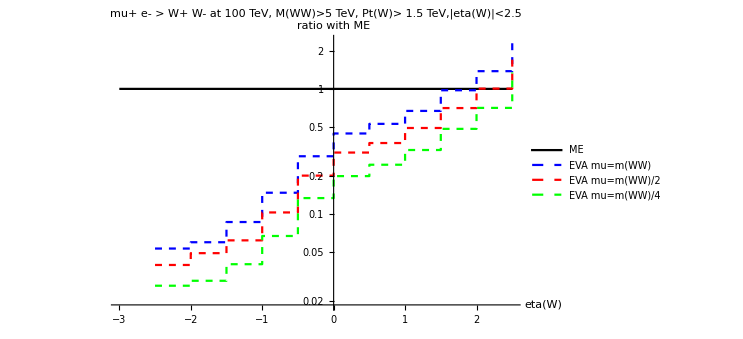

```mathematica
plotmWW=ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio1=ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio2=ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalfLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterLePDF,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 





plotetaW=ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio1=ListLogPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZ,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalf,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarter,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio2=ListLogPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalfLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarterLePDF,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 
dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotDistr/WW_WW/";
run="100TeVcuts/";
Export[dir<>run<>"plotmWW.pdf",plotmWW];
Export[dir<>run<>"plotmWWratio1.pdf",plotmWWratio1];
Export[dir<>run<>"plotmWWratio2.pdf",plotmWWratio2];
Export[dir<>run<>"plotetaW.pdf",plotetaW];
Export[dir<>run<>"plotetaWratio1.pdf",plotetaWratio1];
Export[dir<>run<>"plotetaWratio2.pdf",plotetaWratio2];
```

```mathematica
Plus@@Map[#[[2]]&,etaW]
Plus@@Map[#[[2]]&,Mnunu]
Plus@@Map[#[[2]]&,MWW]
Plus@@Map[#[[2]]&,etaWZZ]
```

1082.98

1082.98

1082.98

686.26

```mathematica
Plus@@Map[#[[2]]*#[[1]]&,ptnu]/Plus@@Map[#[[2]]&,ptnu]
Plus@@Map[#[[2]]&,ptnu]
```

656.108

1082.98

M(WW)>500 GeV con anche Pt(W)> 150 GeV e |eta(W)|<2.5.

```mathematica
(*namerun="Mnunu300"*)
namerun="MWW500_ptnu150_eta2half"
```

MWW500_ptnu150_eta2half

```mathematica
namefolder="mupem_to_nunuWpWm_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
ptnu=prova[4];
etanu=prova[5];
Mnunu=prova[15];
MWW =prova[14];
etaW=prova[13];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="WW_WpWm_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZ =prova[10];
etaWZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalf =prova[10];
etaWZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarter =prova[10];
etaWZZmuquarter=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterpt"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterpt"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterpt =prova[10];
etaWZZmuquarterpt=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuLePDF =prova[10];
etaWZZmuLePDF=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalfLePDF =prova[10];
etaWZZmuhalfLePDF=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterLePDF =prova[10];
etaWZZmuquarterLePDF=prova[6];


(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]

MWWZZmuLePDF =prova[10];
etaWZZmuLePDF=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalfLePDF =prova[10];
etaWZZmuhalfLePDF=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterLePDF =prova[10];
etaWZZmuquarterLePDF=prova[6];*)

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZptmu =prova[10];
etaWZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4","WW Eva mu=sqrtshat","WW Eva mu=sqrtshat/2","WW Eva mu=sqrtshat/4","WW Eva mu=sqrtshat/4 pt evol", "WW Eva mu=sqrtshat a la LePDF", "WW Eva mu=sqrtshat/2 a la LePDF", "WW Eva mu=sqrtshat/4 a la LePDF"};
plotstyle={Thick,Dashed,Dashed,Dashed,Dashed,Dotted,Dotted,Dotted}
```

{Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{0,Small}],Dashing[{0,Small}],Dashing[{0,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV";
```

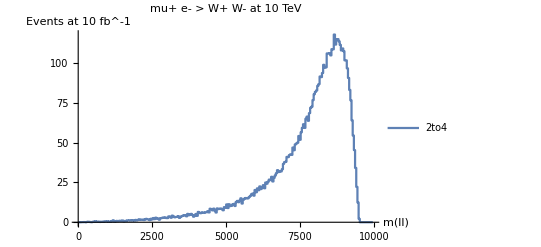

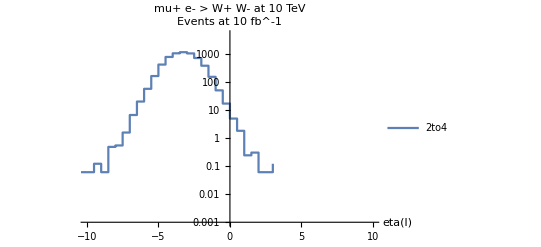

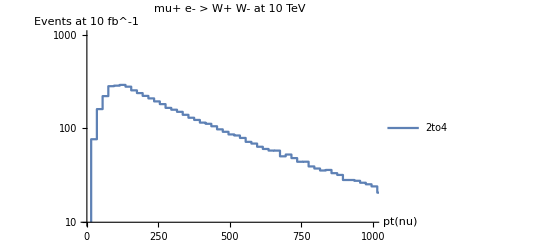

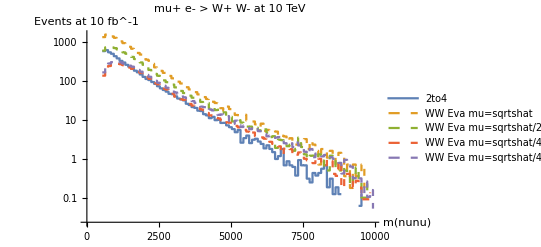

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

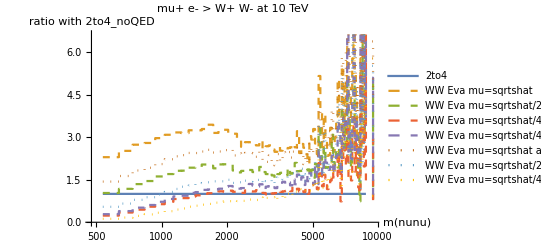

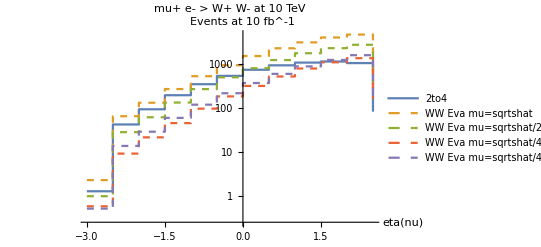

```mathematica
ListPlot[{joinbin[Mnunu,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etanu,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[ptnu,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] 


ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10],joinbin[MWWZZmuquarterpt,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterpt,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalfLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterLePDF,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter,etaWZZmuquarterpt},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME","EVA mu=m(WW) with only Log[mu/MV]","EVA mu=m(WW)/2 with only Log[mu/MV]","EVA mu=m(WW)/4 with only Log[mu/MV]", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4"};
plotlegend2={"ME", "EVA mu=m(WW)", "EVA mu=m(WW)/2", "EVA mu=m(WW)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV, M(WW)>500 GeV, Pt(W)> 150 GeV,|eta(W)|<2.5";
```

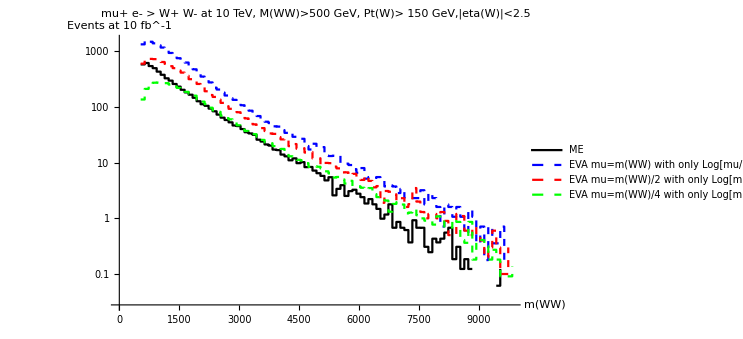

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

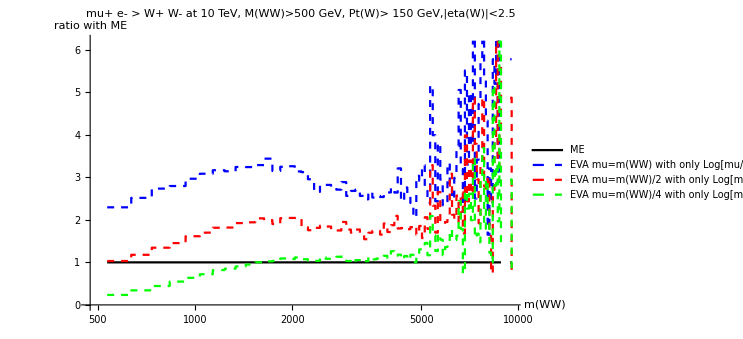

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

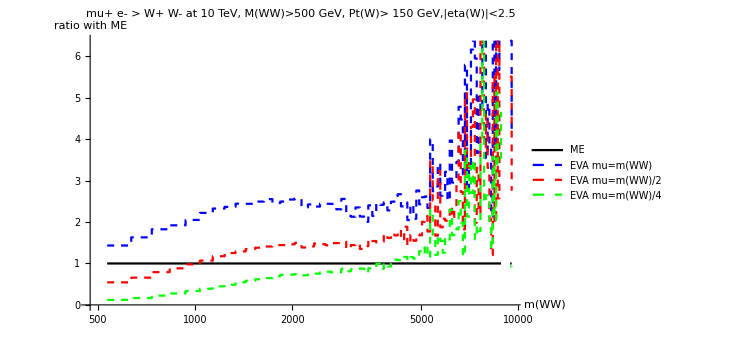

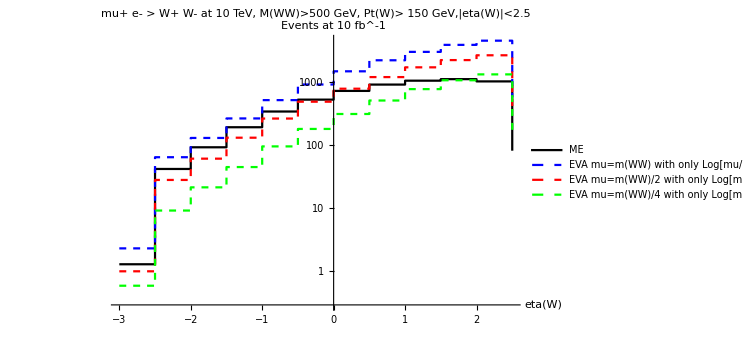

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

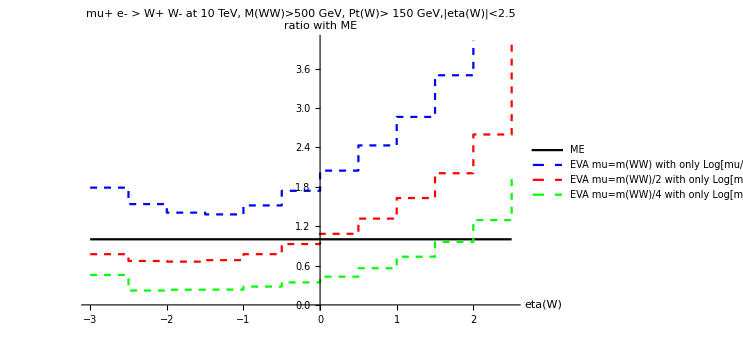

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

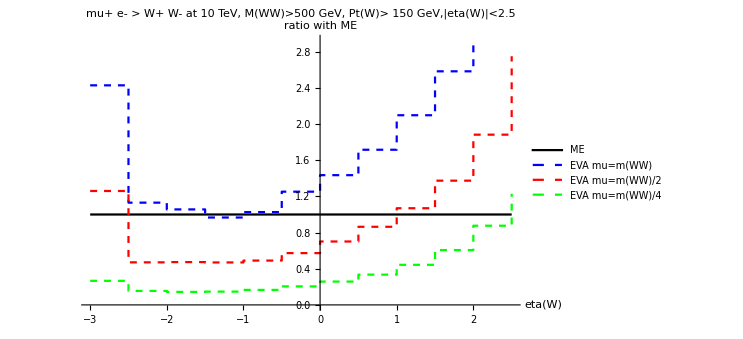

```mathematica
plotmWW=ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio1=ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmWWratio2=ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalfLePDF,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterLePDF,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(WW)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 





plotetaW=ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio1=ListPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZ,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalf,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarter,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetaWratio2=ListPlot[{rapp[joinbin[etaW,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuhalfLePDF,1],joinbin[etaW,1]],rapp[joinbin[etaWZZmuquarterLePDF,1],joinbin[etaW,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(W)","ratio with ME"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 
dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotDistr/WW_WW/";
run="10TeVcuts/";
Export[dir<>run<>"plotmWW.pdf",plotmWW];
Export[dir<>run<>"plotmWWratio1.pdf",plotmWWratio1];
Export[dir<>run<>"plotmWWratio2.pdf",plotmWWratio2];
Export[dir<>run<>"plotetaW.pdf",plotetaW];
Export[dir<>run<>"plotetaWratio1.pdf",plotetaWratio1];
Export[dir<>run<>"plotetaWratio2.pdf",plotetaWratio2];
```

```mathematica
rapp[joinbin[etaW,10],joinbin[etaW,10]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{-8.25,Indeterminate},{-3.25,1.},{1.75,1.},{6.75,Indeterminate}}

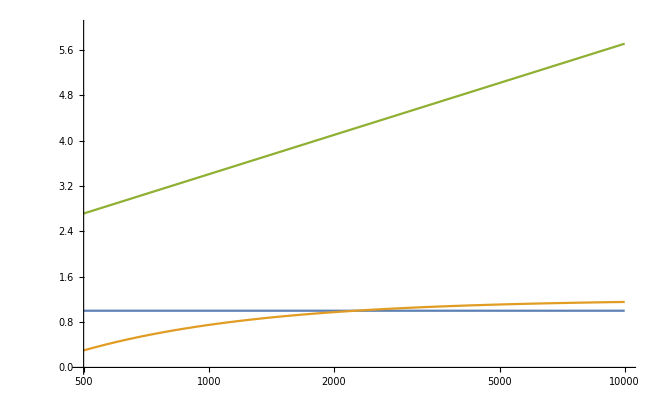

```mathematica
LogLinearPlot[{1,1-5 90/m+0.2,1-Log[90/m]},{m,500,10000},PlotRange->{{500,10000},{0,6}}]
```

```mathematica
Plus@@Map[#[[2]]&,etaW]
Plus@@Map[#[[2]]&,Mnunu]
Plus@@Map[#[[2]]&,MWW]
Plus@@Map[#[[2]]&,etaWZZ]
```

6116.79

6116.79

6116.79

17662.3

```mathematica
Plus@@Map[#[[2]]*#[[1]]&,ptnu]/Plus@@Map[#[[2]]&,ptnu]
Plus@@Map[#[[2]]&,ptnu]
```

436.425

6116.79

ONLY W_L W_L IN THE FINAL STATE!!!


M(WW)>500 GeV con anche Pt(W)> 150 GeV e |eta(W)|<2.5.

```mathematica
(*namerun="Mnunu300"*)
namerun="MWW500_ptnu150_eta2half"
```

MWW500_ptnu150_eta2half

```mathematica
namefolder="mupem_to_LL_nunuWpWm_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
ptnu=prova[4];
etanu=prova[5];
Mnunu=prova[15];
MWW =prova[14];
etaW=prova[13];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="WW_LL_WpWm_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZ =prova[10];
etaWZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalf =prova[10];
etaWZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarter =prova[10];
etaWZZmuquarter=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterpt"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterpt"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterpt =prova[10];
etaWZZmuquarterpt=prova[6];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZptmu =prova[10];
etaWZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4","WW Eva mu=sqrtshat","WW Eva mu=sqrtshat/2","WW Eva mu=sqrtshat/4","WW Eva mu=sqrtshat/4 pt evol"};
plotstyle={Thick,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV";
```

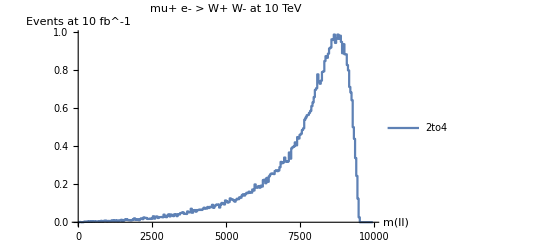

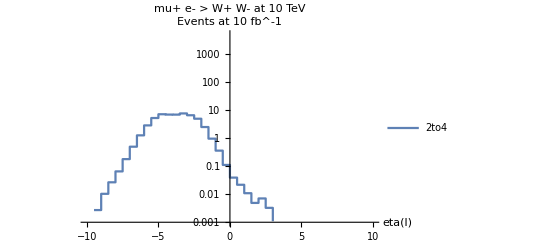

-Graphics-

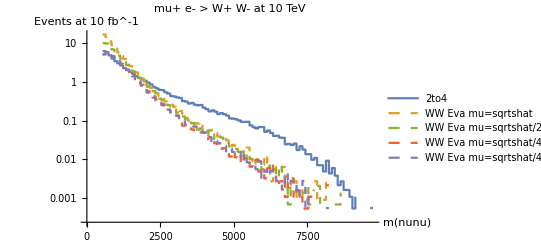

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

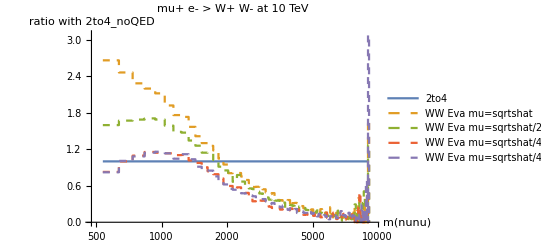

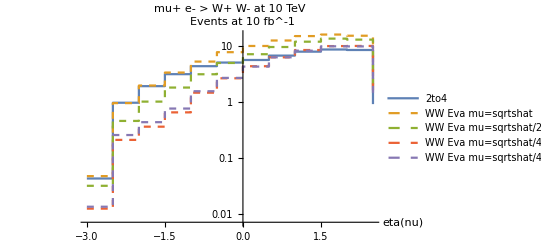

```mathematica
ListPlot[{joinbin[Mnunu,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etanu,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[ptnu,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] 


ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10],joinbin[MWWZZmuquarterpt,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterpt,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter,etaWZZmuquarterpt},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etaW]
Plus@@Map[#[[2]]&,Mnunu]
Plus@@Map[#[[2]]&,MWW]
Plus@@Map[#[[2]]&,etaWZZ]
```

54.4237

54.4237

54.4237

91.1741

```mathematica
Plus@@Map[#[[2]]*#[[1]]&,ptnu]/Plus@@Map[#[[2]]&,ptnu]
Plus@@Map[#[[2]]&,ptnu]
```

321.329

54.4236

ONLY W_T W_T IN THE FINAL STATE!!!


M(WW)>500 GeV con anche Pt(W)> 150 GeV e |eta(W)|<2.5.

```mathematica
(*namerun="Mnunu300"*)
namerun="MWW500_ptnu150_eta2half"
```

MWW500_ptnu150_eta2half

```mathematica
namefolder="mupem_to_TT_nunuWpWm_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
ptnu=prova[4];
etanu=prova[5];
Mnunu=prova[15];
MWW =prova[14];
etaW=prova[13];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="WW_TT_WpWm_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZ =prova[10];
etaWZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuhalf =prova[10];
etaWZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarter =prova[10];
etaWZZmuquarter=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterpt"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterpt"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZmuquarterpt =prova[10];
etaWZZmuquarterpt=prova[6];



(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MWWZZptmu =prova[10];
etaWZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4","WW Eva mu=sqrtshat","WW Eva mu=sqrtshat/2","WW Eva mu=sqrtshat/4","WW Eva mu=sqrtshat/4 pt evol"};
plotstyle={Thick,Dashed,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > W+ W- at 10 TeV";
```

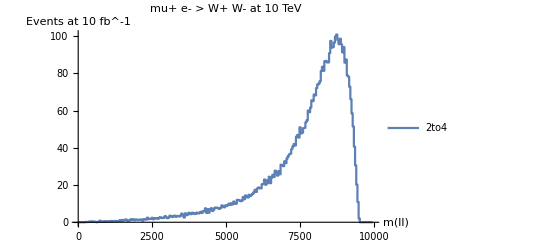

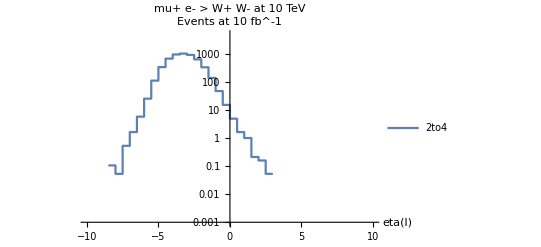

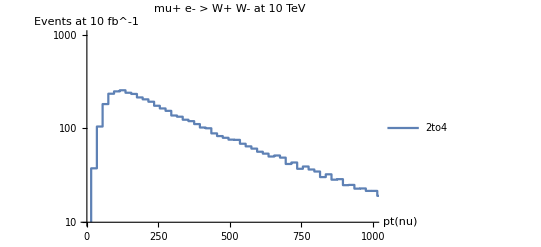

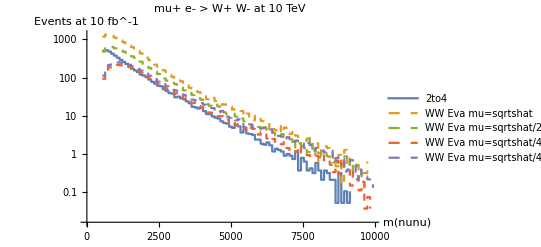

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

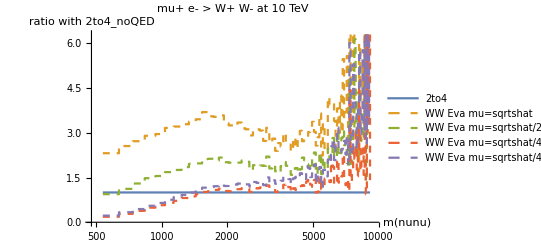

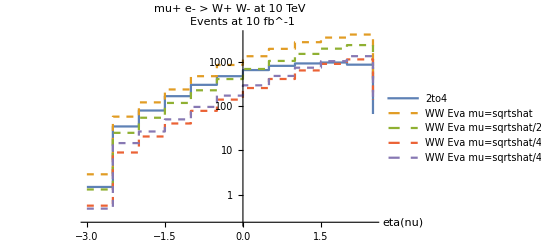

```mathematica
ListPlot[{joinbin[Mnunu,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etanu,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[ptnu,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] 


ListLogPlot[{joinbin[MWW,10],joinbin[MWWZZ,10],joinbin[MWWZZmuhalf,10],joinbin[MWWZZmuquarter,10],joinbin[MWWZZmuquarterpt,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MWW,10],joinbin[MWW,10]],rapp[joinbin[MWWZZ,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuhalf,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarter,10],joinbin[MWW,10]],rapp[joinbin[MWWZZmuquarterpt,10],joinbin[MWW,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etaW,etaWZZ,etaWZZmuhalf,etaWZZmuquarter,etaWZZmuquarterpt},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etaW]
Plus@@Map[#[[2]]&,Mnunu]
Plus@@Map[#[[2]]&,MWW]
Plus@@Map[#[[2]]&,etaWZZ]
```

5341.14

5341.14

5341.14

16038.3

```mathematica
Plus@@Map[#[[2]]*#[[1]]&,ptnu]/Plus@@Map[#[[2]]&,ptnu]
Plus@@Map[#[[2]]&,ptnu]
```

444.797

5341.14